## Temperature

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=2Pi 377.107385*10^12;
dopp=2 w0/c*Sqrt[2 Log[2 ]k*T1/MRb]/(2Pi);
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

## 3Level

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α1∉Reals,Integrate[(ⅇ^(-v^2/u^2))/(v+α1),{v,-∞,∞}]]//FullSimplify*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (ⅈ π Erfc[I α1/u])
(*Int=A (π 2 /Sqrt[π] DawsonF[α1/u]-Log[-1/α1] ⅇ^(-α1^2/u^2)-Log[α1] ⅇ^(-α1^2/u^2))//Simplify*)
]
```

## 4Level

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-((d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)) )/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ));
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα= CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (-I π (Erfc[-I α1/u]))+ⅇ^(-α2^2/u^2) (Zα+α2) (-I π (Erfc[-I α2/u])))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

## Define function

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
(*sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];*)
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.003,0.003,0.00004]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

```mathematica
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

## Rubidum 85

```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\85F11"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,max][[1]],#[ll,min][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,max][[1]],#[ll,min][[-1]]}&@Position]];

wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,1,100}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-500,Length[yaxis1]}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[
GaussianFilter[yaxis2,10]
,16,0.00002],1500<#[[1]]<4500&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],0},{loc[[-1,1]],0.361}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],GaussianFilter[yaxis1/gg,10],yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

```mathematica
Manipulate[
ListPlot[{GaussianFilter[data2[[i]][[All,8]],10],
Select[FindPeaks[
GaussianFilter[data2[[i]][[All,8]],10]
,16,0.00002],1500<#[[1]]<4500&]},PlotStyle->{Black,{Red,AbsolutePointSize[5]}}]
,{{i,62},1,Length[data2],1}]
```

```mathematica
Manipulate[ListPlot[Transpose[f[data2[[i]]][[{4,2}]]],PlotRange->{{-1,2},{0,1.2}},Joined->True],{{i,2},1,Length[data2],1}]
```

Take::take: Cannot take positions 6164 through 310 in {0.0624,0.0632,0.0624,0.0624,0.0632,0.0624,0.0624,0.0632,0.0632,0.0624,0.0624,0.0632,0.0624,0.0624,0.0632,0.0632,0.0624,0.0624,0.0624,0.0624,0.0624,0.0616,0.0632,0.0624,0.0632,0.0624,0.0632,0.0632,0.0632,0.0632,0.0632,0.064,0.0632,0.0624,0.0624,0.0632,0.0632,0.0616,0.0632,0.0624,0.0624,0.0616,0.0624,0.0624,0.0624,0.0624,0.0624,0.0624,0.0616,0.0632,«6199»}.

Take::take: Cannot take positions 6164 through 310 in {5.58,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.58,5.58,5.58,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,«6199»}.

Part::partw: Part 3 of Take[{0.0624,0.0632,0.0624,0.0624,0.0632,0.0624,0.0624,0.0632,0.0632,0.0624,0.0624,0.0632,0.0624,0.0624,0.0632,0.0632,0.0624,0.0624,0.0624,0.0624,0.0624,0.0616,0.0632,0.0624,0.0632,0.0624,0.0632,0.0632,0.0632,0.0632,0.0632,0.064,0.0632,0.0624,0.0624,0.0632,0.0632,0.0616,0.0632,0.0624,0.0624,0.0616,0.0624,0.0624,0.0624,0.0624,0.0624,0.0624,0.0616,0.0632,«6199»},{6164,310}] does not exist.

Part::partw: Part 4 of Take[{0.0624,0.0632,0.0624,0.0624,0.0632,0.0624,0.0624,0.0632,0.0632,0.0624,0.0624,0.0632,0.0624,0.0624,0.0632,0.0632,0.0624,0.0624,0.0624,0.0624,0.0624,0.0616,0.0632,0.0624,0.0632,0.0624,0.0632,0.0632,0.0632,0.0632,0.0632,0.064,0.0632,0.0624,0.0624,0.0632,0.0632,0.0616,0.0632,0.0624,0.0624,0.0616,0.0624,0.0624,0.0624,0.0624,0.0624,0.0624,0.0616,0.0632,«6199»},{6164,310}] does not exist.

Part::partw: Part 5 of Take[{0.0624,0.0632,0.0624,0.0624,0.0632,0.0624,0.0624,0.0632,0.0632,0.0624,0.0624,0.0632,0.0624,0.0624,0.0632,0.0632,0.0624,0.0624,0.0624,0.0624,0.0624,0.0616,0.0632,0.0624,0.0632,0.0624,0.0632,0.0632,0.0632,0.0632,0.0632,0.064,0.0632,0.0624,0.0624,0.0632,0.0632,0.0616,0.0632,0.0624,0.0624,0.0616,0.0624,0.0624,0.0624,0.0624,0.0624,0.0624,0.0616,0.0632,«6199»},{6164,310}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Fit::fitd: First argument {{1,{0.0624,0.0632,0.0624,0.0624,0.0632,0.0624,0.0624,0.0632,0.0632,0.0624,0.0624,0.0632,0.0624,0.0624,0.0632,0.0632,0.0624,0.0624,0.0624,0.0624,0.0624,0.0616,0.0632,0.0624,0.0632,0.0624,0.0632,0.0632,0.0632,0.0632,0.0632,0.064,0.0632,0.0624,0.0624,0.0632,0.0632,0.0616,0.0632,0.0624,0.0624,0.0616,0.0624,0.0624,0.0624,0.0624,0.0624,0.0624,0.0616,0.0632,«6199»}},{2,{6164,310}},«48»,«551»} in Fit is not a list or a rectangular array.

General::ivar: 1 is not a valid variable.

General::ivar: 2 is not a valid variable.

GaussianFilter::arg1: The first argument Take[{5.58,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.58,5.58,5.58,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,«6199»},{6164,310}] is neither a rectangular array nor an image.

FindPeaks::arg: The argument GaussianFilter[Take[{5.58,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.58,5.58,5.58,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.54,5.58,5.54,5.54,5.54,«6199»},{6164,310}],10] at position 1 is not a consistent list of real values.

Part::partd: Part specification 16⟦1⟧ is longer than depth of object.

Part::partd: Part specification 0.00002⟦1⟧ is longer than depth of object.

FindPeaks::argb: FindPeaks called with 0 arguments; between 1 and 4 arguments are expected.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

{0.636725,0.639901,0.66731,0.674329,0.667808,0.694521,0.70758,0.696752,0.679945,0.709429,0.693684,0.712437,0.709074,0.716864,0.743021,0.710501,0.729227,0.722045,0.721196,0.734419,0.733136,0.718431,0.751183,0.754288,0.743229,0.746981,0.751656,0.751251,0.75013,0.745624,0.750275,0.744427,0.743976,0.749496,0.765288,0.757443,0.766202,0.765752,0.760205,0.747148,0.759932,0.759053,0.761859,0.752258,0.754261,0.760051,0.748734,0.767423,0.753312,0.75447,0.762398,0.767371}

{0.514775,0.508047,0.505168,0.502372,0.491164,0.480834,0.494902,0.485853,0.49222,0.481965,0.479442,0.494552,0.489505,0.48135,0.476866,0.477204,0.486706,0.491235,0.487083,0.478102,0.481594,0.491111,0.488701,0.482923,0.49261,0.494719,0.497917,0.473989,0.487133,0.471823,0.46281,0.463907,0.488127,0.478173,0.476849,0.474735,0.470335,0.495877,0.486693,0.473808,0.48523,0.471941,0.469051,0.4897,0.48161,0.487289,0.458397,0.498835,0.499702,0.474623,0.518232,0.5016}

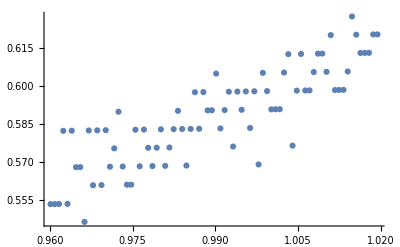

```mathematica
EITmax85=Table[Select[Transpose[f[data2[[i]]][[{4,2}]]],0.96<#[[1]]<1.02&][[All,2]]//Max,{i,1,Length[data]-1,1}]
EITmin85=Table[Select[Transpose[f[data2[[i]]][[{4,2}]]],0.96<#[[1]]<1.02&][[All,2]]//Min,{i,1,Length[data]-1,1}]
```

```mathematica
abs85=Select[Transpose[f[data2[[-1]]][[{4,2}]]],0.96<#[[1]]<1.02&][[All,2]]//Mean;
```

```mathematica
power={1,1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10,12,12,14,14,16,16,18,18,20,20,22.5,22.5,25,25,27.5,27.5,30,30,35,35,40,40,45,45,50,50,60,60,70,70,80,80};
```

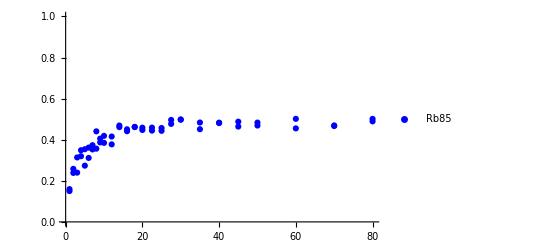

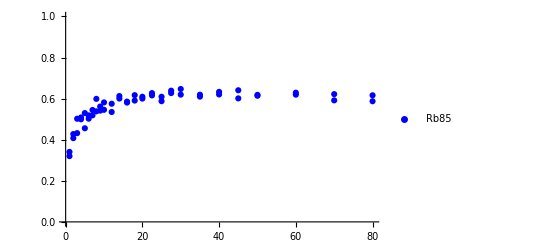

```mathematica
rb85=ListPlot[Transpose[{power,1-(12.531885282826405 794.76728224*10^-9 Log[EITmax85])/(12.531885282826405 794.76728224*10^-9 Log[abs85])}],PlotRange->{0,1},PlotStyle->Blue,PlotLegends->{"Rb85"}]
rb85min=ListPlot[Transpose[{power,1-(12.531885282826405 794.76728224*10^-9 Log[EITmax85])/(12.531885282826405 794.76728224*10^-9 Log[EITmin85])}],PlotRange->{0,1},PlotStyle->Blue,PlotLegends->{"Rb85"}]
```

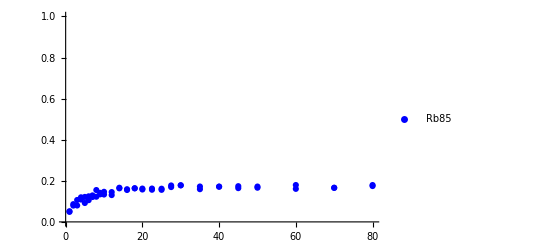

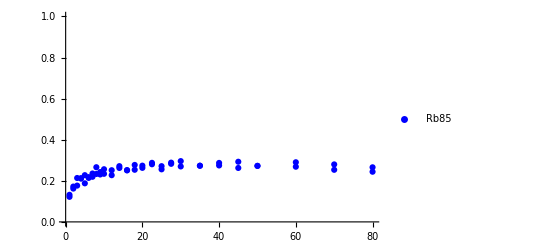

```mathematica
rb85sub=ListPlot[Transpose[{power,EITmax85-abs85}],PlotRange->{0,1},PlotStyle->Blue,PlotLegends->{"Rb85"}]
rb85submin=ListPlot[Transpose[{power,EITmax85-EITmin85}],PlotRange->{0,1},PlotStyle->Blue,PlotLegends->{"Rb85"}]
```

## Rubidum 87

```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-24\\87power"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,max][[1]],#[ll,min][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,max][[1]],#[ll,min][[-1]]}&@Position]];
wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,1,200}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-500,Length[yaxis1]}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[yaxis2,9,0.00005],1200<#[[1]]<3500&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-.816},{loc[[-1,1]],0}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],yaxis1/gg,yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

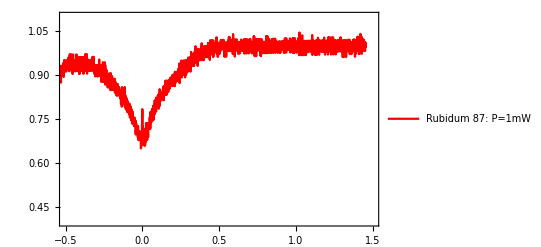

```mathematica
Rb87p1=ListPlot[
Transpose[{f[data2[[1]]][[4]],f[data2[[1]]][[2]]}]
,PlotRange->{{-0.5,1.5},{0.4,1.1}},Frame->True,Joined->True,PlotLegends->{"Rubidum 87: P=1mW"},Axes->False,Frame->True,PlotStyle->Red]
```

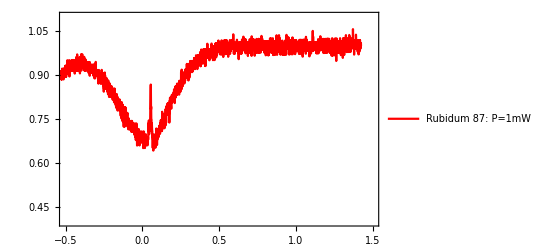

```mathematica
Rb87p10=ListPlot[
Transpose[{f[data2[[20]]][[4]],f[data2[[20]]][[2]]}]
,PlotRange->{{-0.5,1.5},{0.4,1.1}},Frame->True,Joined->True,PlotLegends->{"Rubidum 87: P=1mW"},Axes->False,Frame->True,PlotStyle->Red]
```

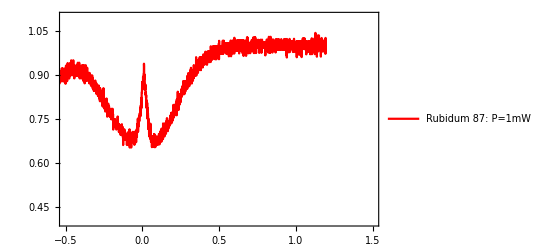

```mathematica
Rb87p80=ListPlot[
Transpose[{f[data2[[-2]]][[4]],f[data2[[-2]]][[2]]}]
,PlotRange->{{-0.5,1.5},{0.4,1.1}},Frame->True,Joined->True,PlotLegends->{"Rubidum 87: P=1mW"},Axes->False,Frame->True,PlotStyle->Red]
```

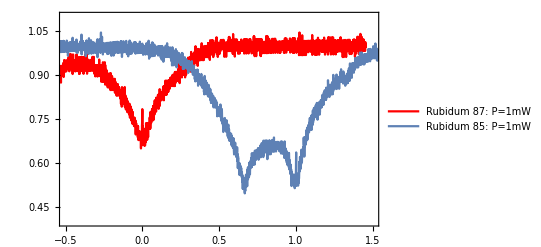

```mathematica
Show[Rb87p1,Rb85p1]
```

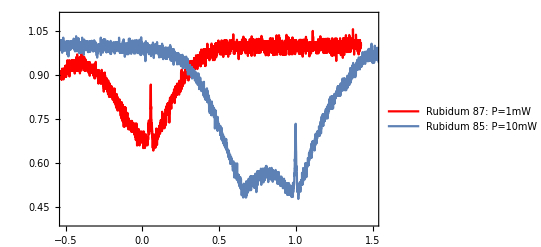

```mathematica
Show[Rb87p10,Rb85p10]
```

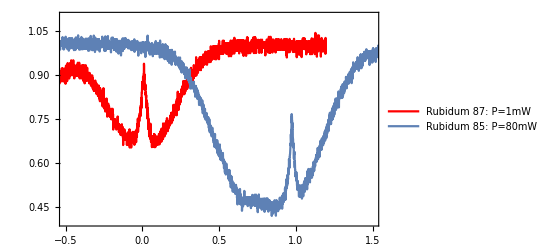

```mathematica
Show[Rb87p80,Rb85p80]
```

```mathematica
EITmax87=Table[Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.1&][[All,2]]//Max,{i,1,Length[data]-1,1}]
EITmin87=Table[Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.1&][[All,2]]//Min,{i,1,Length[data]-1,1}]
```

{0.823399,0.828718,0.809486,0.803134,0.816831,0.813843,0.837912,0.831469,0.848236,0.826872,0.856695,0.846044,0.856902,0.886301,0.867909,0.860688,0.871409,0.871093,0.87643,0.867907,0.884038,0.870866,0.880137,0.88198,0.895963,0.884955,0.89316,0.897721,0.897539,0.877515,0.900594,0.895854,0.893767,0.903589,0.922521,0.908167,0.912399,0.904083,0.902287,0.9137,0.899981,0.916962,0.903374,0.925303,0.926671,0.910904,0.899034,0.909838,0.914975,0.915378,0.914098,0.938985}

{0.6503,0.650342,0.654794,0.639272,0.645979,0.653072,0.640411,0.651703,0.639851,0.654524,0.653107,0.623876,0.63675,0.636804,0.6493,0.632647,0.633507,0.633274,0.641658,0.642944,0.64693,0.642638,0.6275,0.628808,0.627847,0.645271,0.618771,0.644114,0.62563,0.6179,0.623845,0.636235,0.634811,0.63518,0.636053,0.639277,0.606861,0.633603,0.628708,0.620525,0.63911,0.638071,0.646844,0.634085,0.626032,0.633278,0.645484,0.647052,0.633053,0.639207,0.649826,0.654642}

```mathematica
abs87=Select[Transpose[f[data2[[-1]]][[{4,2}]]],-0.02<#[[1]]<0.1&][[All,2]]//Mean;
```

```mathematica
power={1,1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10,12,12,14,14,16,16,18,18,20,20,22.5,22.5,25,25,27.5,27.5,30,30,35,35,40,40,45,45,50,50,60,60,70,70,80,80};
```

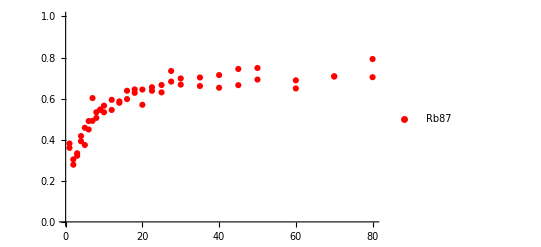

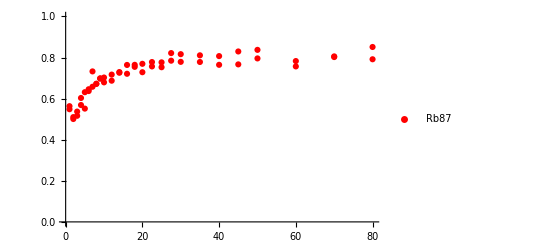

```mathematica
rb87=ListPlot[Evaluate[Transpose[{power,1-Log[EITmax87]/Log[abs87]}]],PlotRange->{0,1},PlotStyle->Red,PlotLegends->{"Rb87"}]
rb87min=ListPlot[Evaluate[Transpose[{power,1-Log[EITmax87]/Log[EITmin87]}]],PlotRange->{0,1},PlotStyle->Red,PlotLegends->{"Rb87"}]
```

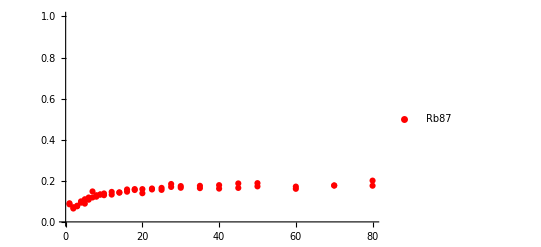

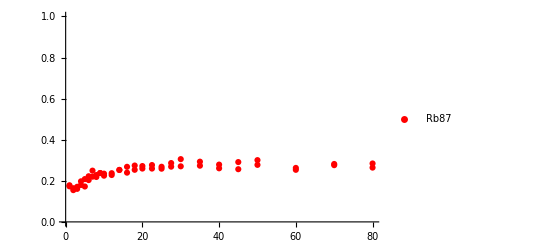

```mathematica
rb87sub=ListPlot[Transpose[{power,EITmax87-abs87}],PlotRange->{0,1},PlotStyle->Red,PlotLegends->{"Rb87"}]
rb87submin=ListPlot[Transpose[{power,EITmax87-EITmin87}],PlotRange->{0,1},PlotStyle->Red,PlotLegends->{"Rb87"}]
```

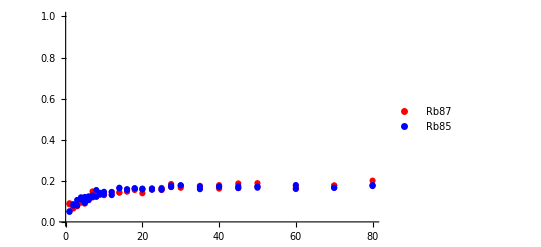

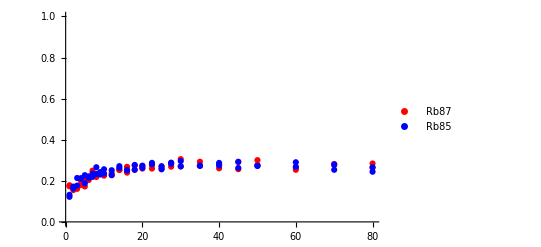

```mathematica
Show[rb87sub,rb85sub]
Show[rb87submin,rb85submin]
```

# Plot

```mathematica
Off[Power::infy];Off[Infinity::indet];
T=23;
γ=1.4;
Module[{list85,list185,list3,list4,EIT85,ABS85,EIT1,ABS1},
Tvw41={};Tvw3185={};
Do[
list85=Lev4DoppTestsc[T,p/1000,0.9/1000,γ*10^6,0,0,361];
list185=Lev4DoppTestsc[T,0/1000,0.9/1000,γ*10^6,0,0,361];

list3=Lev4DoppTestsc87[T,p/1000,0.9/1000,γ*10^6,0,0,816];
list4=Lev4DoppTestsc87[T,0/1000,0.9/1000,γ*10^6,0,0,816];

EIT85=Min[DeleteCases[list85,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS85=list185[[Position[list85,EIT85][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41=Append[Tvw41,{p,1-EIT1/ABS1}];
Tvw3185=Append[Tvw3185,{p,1-EIT85/ABS85}];

,{p,0,80,5}]
]
```

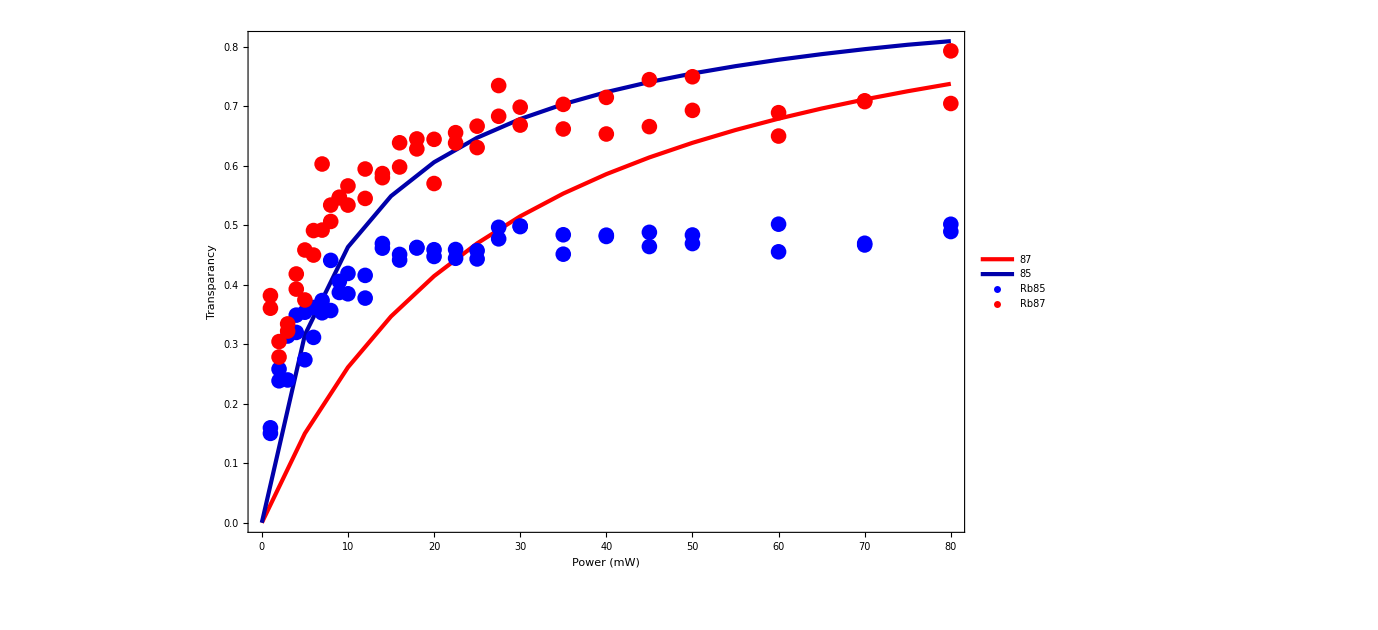

```mathematica
tr=ListPlot[{Tvw41,Tvw3185},Joined->True,PlotLegends->{87,85},ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Darker[Blue]}}
,Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy ",50,Black]}];
Show[tr,rb85,rb87]
```

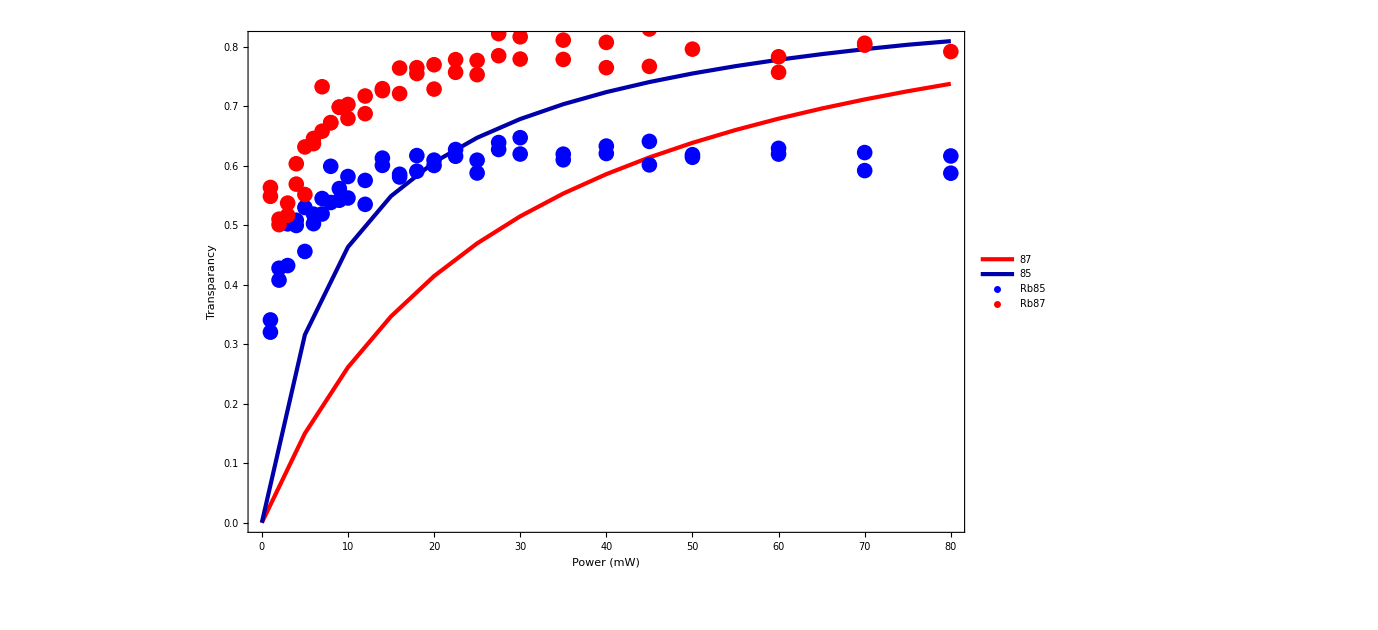

```mathematica
tr=ListPlot[{Tvw41,Tvw3185},Joined->True,PlotLegends->{87,85},ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Darker[Blue]}}
,Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy ",50,Black]}];
Show[tr,rb85min,rb87min]
```

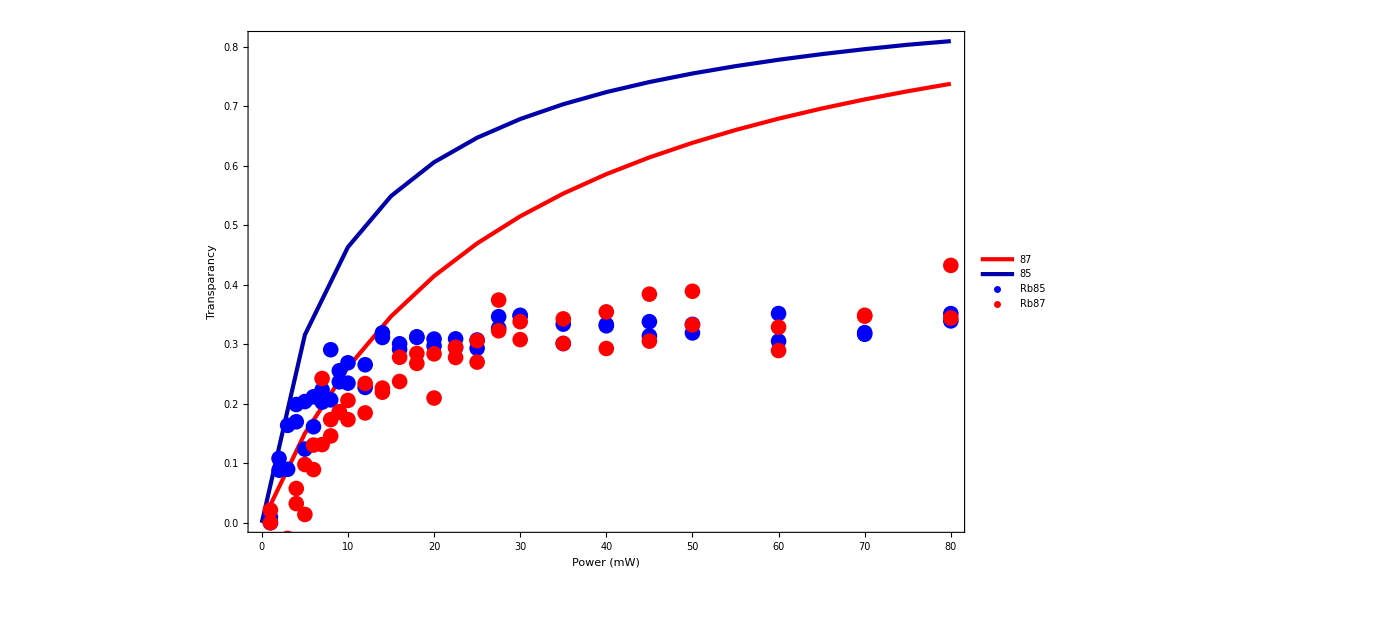

```mathematica
rb87t=ListPlot[Evaluate[Transpose[{power,1-Log[EITmax87]/Log[abs87]-0.3604286017162307}]],PlotRange->{0,1},PlotStyle->Red,PlotLegends->{"Rb87"}];
rb85t=ListPlot[Transpose[{power,1-Log[EITmax85]/Log[abs85]-0.15013075665125342}],PlotRange->{0,1},PlotStyle->Blue,PlotLegends->{"Rb85"}];
tr=ListPlot[{Tvw41,Tvw3185},Joined->True,PlotLegends->{87,85},ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Darker[Blue]}}
,Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy ",50,Black]}];
Show[tr,rb85t,rb87t]
```

```mathematica
1-(Log[EITmax87]/Log[abs87])[[-1]]
```

```mathematica
0.84-0.7927851927405548
```

0.0472148

```mathematica
1-(Log[EITmax85]/Log[abs85])[[-1]]
0.84-0.5014959534381679
```

0.501496

0.338504

```mathematica
Fit[Take[Transpose[{power,1-Log[EITmax87]/Log[abs87]}],{-10,-1}],1,x]
Fit[Take[Transpose[{power,1-Log[EITmax85]/Log[abs85]}],{-10,-1}],1,x]
```

0.710454

0.478833

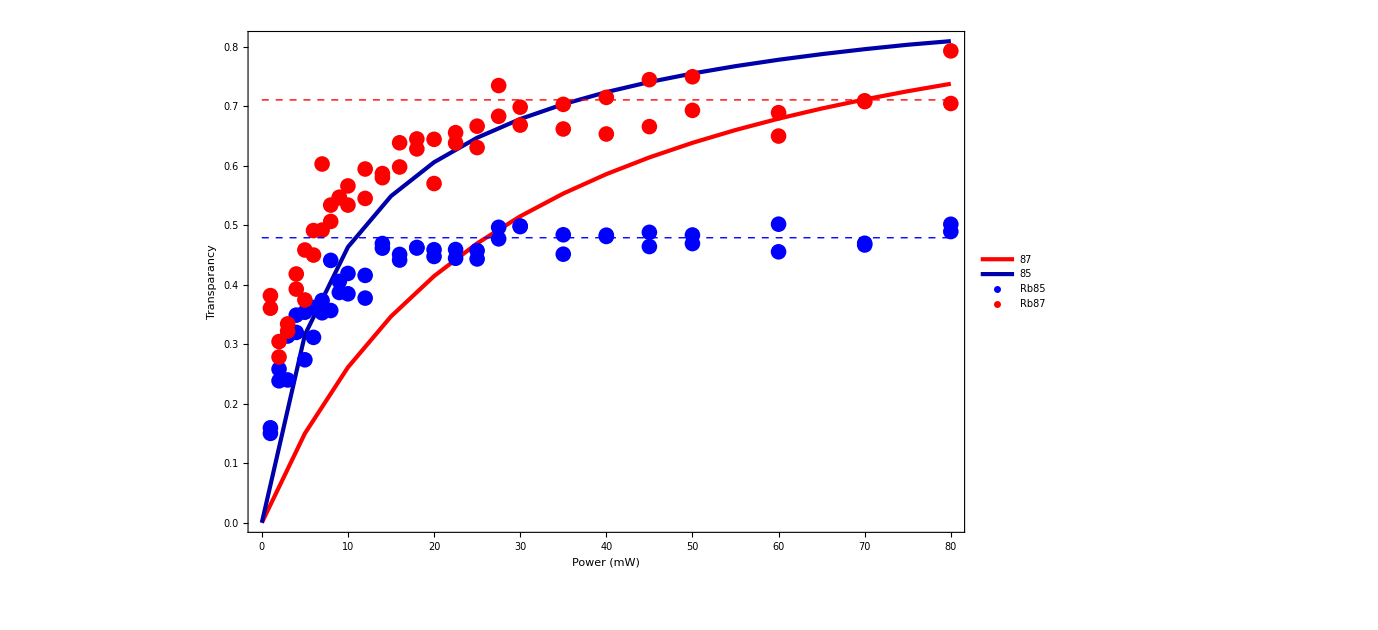

```mathematica
fit87=Fit[Take[Transpose[{power,1-Log[EITmax87]/Log[abs87]}],{-10,-1}],1,x];
fit85=Fit[Take[Transpose[{power,1-Log[EITmax85]/Log[abs85]}],{-10,-1}],1,x];
rb87d=ListPlot[Evaluate[Transpose[{power,1-Log[EITmax87]/Log[abs87]}]],PlotRange->{0,1},PlotStyle->Red,PlotLegends->{"Rb87"}];
rb85d=ListPlot[Evaluate[Transpose[{power,1-Log[EITmax85]/Log[abs85]}]],PlotRange->{0,1},PlotStyle->Blue,PlotLegends->{"Rb85"}];
tr=ListPlot[{Tvw41,Tvw3185},Joined->True,PlotLegends->{87,85},ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Darker[Blue]}}
,Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy ",50,Black]},
Epilog->{{Red,Dashed,Line[{{0,fit87},{80,fit87}}]},{Blue,Dashed,Line[{{0,fit85},{80,fit85}}]}}
];
Show[tr,rb85d,rb87d]
```

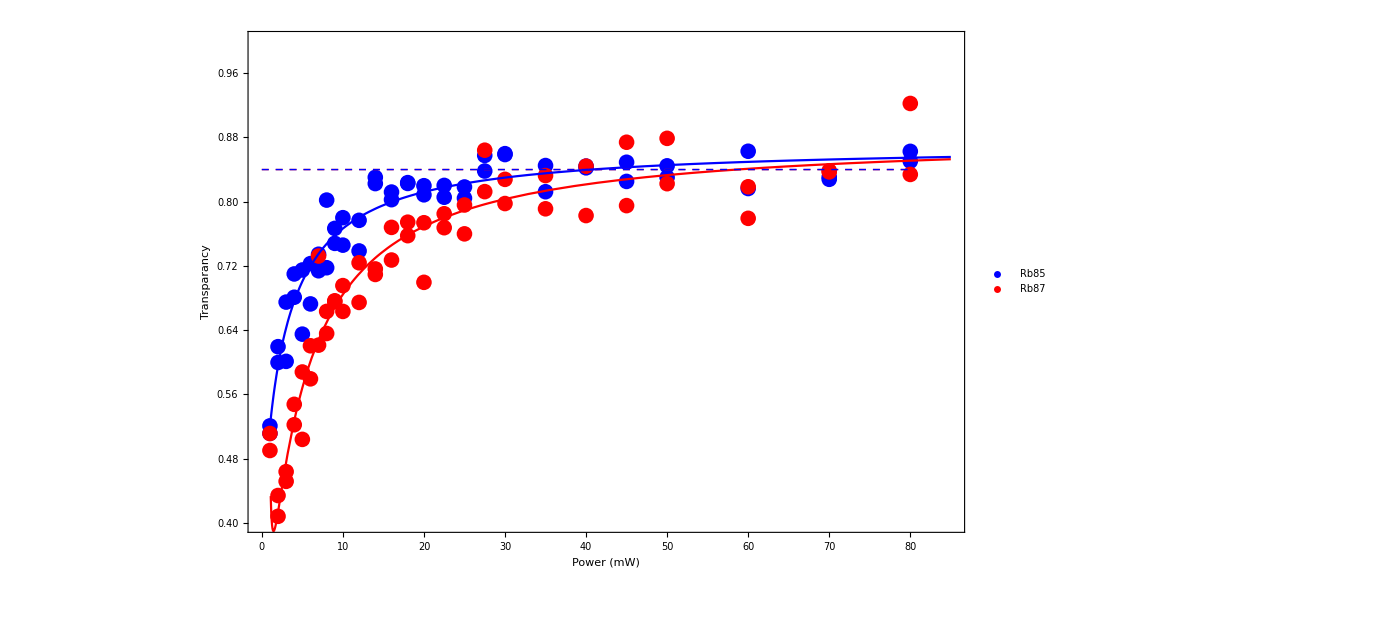

```mathematica
fit87=Fit[Take[Transpose[{power,1-Log[EITmax87]/Log[abs87]}],{-10,-1}],1,x];
fit85=Fit[Take[Transpose[{power,1-Log[EITmax85]/Log[abs85]}],{-10,-1}],1,x];
fit187=NonlinearModelFit[Transpose[{power,1-Log[EITmax87]/Log[abs87]+0.84-fit87}],(a x^2+b x)/(c x^2+d x+e),{a,b,c,d,e},x][x];
fit185=NonlinearModelFit[Transpose[{power,1-Log[EITmax85]/Log[abs85]+0.84-fit85}],(a x^2+b x)/(c x^2+d x+e),{a,b,c,d,e},x][x];
kk=Plot[{fit187,fit185},{x,1.1,85},PlotStyle->{Red,Blue},PlotPoints->30,PlotRange->{0,1}];
rb87d=ListPlot[Evaluate[Transpose[{power,1-Log[EITmax87]/Log[abs87]+(0.84-fit87)}]],PlotRange->{0,1},PlotStyle->Red,PlotLegends->{"Rb87"}];
rb85d=ListPlot[Evaluate[Transpose[{power,1-Log[EITmax85]/Log[abs85]+(0.84-fit85)}]],PlotRange->{0,1},PlotStyle->Blue,PlotLegends->{"Rb85"}];
tr=ListPlot[{{0,0},{0,0}},Joined->True,ImageSize->1020,Joined->True,
PlotRange->{{0,85},{0.4,1}}
,Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy ",50,Black]},
Epilog->{{Red,Dashed,Line[{{0,(0.84)},{80,(0.84)}}]},{Blue,Dashed,Line[{{0,0.84},{80,0.84}}]}}
];
Show[tr,rb85d,rb87d,kk]
```

# Another Plot

```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-24\\85power scan\\P=200"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,max][[1]],#[ll,min][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,max][[1]],#[ll,min][[-1]]}&@Position]];
wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,2000,2700}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-200,Length[yaxis1]}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[yaxis2,9,0.00005],1200<#[[1]]<3500&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-.816},{loc[[-1,1]],0}},{1,x},x]];

{1,yaxis1/gg,yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

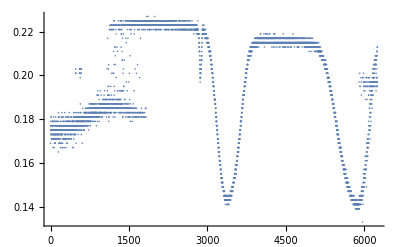

```mathematica
ListPlot[data2[[1]][[All,4]]]
```

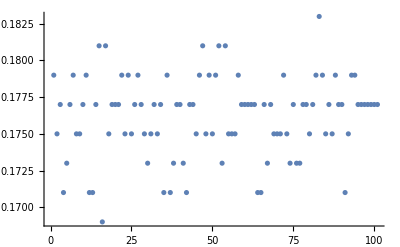

```mathematica
ListPlot[Take[data2[[3]][[All,4]],{500,600}]]
```

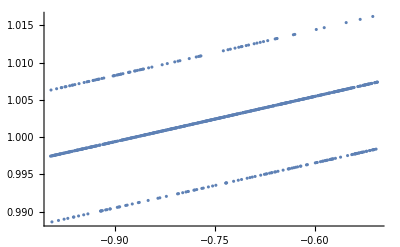

```mathematica
ListPlot[Take[Transpose[f[data2[[i]]][[{4,2}]]],{2000,2700}]]
```

```mathematica
Manipulate[
ListPlot[Take[Transpose[f[data2[[i]]][[{4,2}]]],{2000,-1}]],{i,1,Length[data2],1}]
```

```mathematica
Take[Transpose[f[data2[[1]]][[{4,2}]]],{2500,-500}]//Length
```

1450

```mathematica
Table[i,{l,1,1450}]//Length
```

1450

```mathematica
(Take[Transpose[f[data2[[i]]][[{4,2}]]],{2500,-500}]//Transpose)[[1]]//Length
```

1450

```mathematica
Flatten[{Table[i,{l,1,1450}],Take[Transpose[f[data2[[i]]][[{4,2}]]],{2500,-500}]//Transpose},1]
```

```mathematica
Transpose[Take[Transpose[f[data2[[i]]][[{4,2}]]],{2500,-500}]]//Length
```

```mathematica
Length[Transpose[Take[Transpose[f[data2[[i]]][[{4,2}]]],{2500,-500}]]]
```

2

{{2,-0.328942,1.00585},{2,-0.328194,0.996928},{2,-0.327447,0.996944},{2,-0.326699,1.0059},{2,-0.325951,1.00592},{2,-0.325204,0.996994},{2,-0.324456,0.99701},{2,-0.323709,0.997027},1654,{2,0.913561,0.997419},{2,0.914309,0.988243},{2,0.915056,0.997453},{2,0.915804,0.988276},{2,0.916552,0.988293},{2,0.917299,0.98831},{2,0.918047,0.988327},{2,0.918794,0.988343}}
 |  |  |  |

```mathematica
dataContour=
Flatten[Table[Transpose[{Table[i,{l,1,Length[Transpose[Take[Transpose[f[data2[[i]]][[{4,2}]]],{2500,-500}]][[1]]]}],
Transpose[Take[Transpose[f[data2[[i]]][[{4,2}]]],{2500,-500}]][[1]],Transpose[Take[Transpose[f[data2[[i]]][[{4,2}]]],{2500,-500}]][[2]]}],{i,1,Length[data]}],1]
;
```

{{1,-0.496896,1.01014},{1,-0.496187,1.01015},{1,-0.495479,1.01017},{1,-0.494771,1.00112},{1,-0.494062,1.0102},{1,-0.493354,1.00115},{1,-0.492646,1.01023},{1,-0.491937,1.01024},41571,{28,0.50253,0.991706},{28,0.503229,0.99172},{28,0.503928,0.991734},{28,0.504627,0.991748},{28,0.505326,1.00107},{28,0.506025,0.991776},{28,0.506724,0.982478},{28,0.507423,0.991805}}
 |  |  |  |

```mathematica
dataContour//Length
```

41587

```mathematica
ListContourPlot[dataContour,InterpolationOrder->3]
```

$Aborted

```mathematica
ListContourPlot[RandomChoice[dataContour,InterpolationOrder->3]
```

## test

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.5,0.5,0.004]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]


]
```

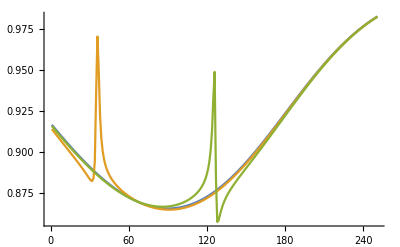

```mathematica
Out[78]
```

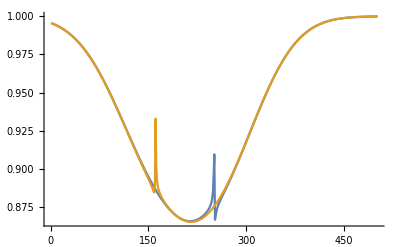

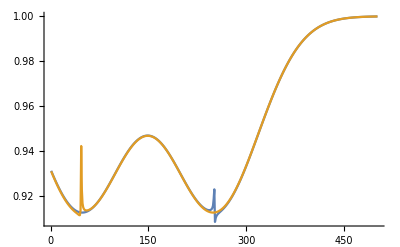

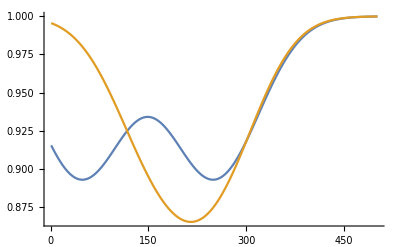

```mathematica
p=5;
ListPlot[{Lev4DoppTestsc[T,p/1000,0.9/1000,γ*10^6,0,0,361],Lev4DoppTestsc[T,p/1000,0.9/1000,γ*10^6,-361*10^6,0,361]},Joined->True]
ListPlot[{Lev4DoppTestsc87[T,p/1000,0.9/1000,γ*10^6,0,0,816],Lev4DoppTestsc87[T,p/1000,0.9/1000,γ*10^6,-816*10^6,0,816]},Joined->True]
ListPlot[{Lev4DoppTestsc87[T+2,0/1000,0.9/1000,γ*10^6,0,0,816],Lev4DoppTestsc[T,0/1000,0.9/1000,γ*10^6,0,0,361]},Joined->True]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-1,1,0.004]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]


]
```

```mathematica
Lev4DoppTestsc87[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-1,1,0.004]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[1/6]*2.5373 10^-29;
d42=Sqrt[1/6]*2.5373 10^-29;
d31=Sqrt[1/18]*2.5373 10^-29;
d41=Sqrt[5/18]*2.5373 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.9788509*10^-9);
wc=2Pi 377.1074635*10^12;
w43=2Pi ((306.246*10^6) +(510.410*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]


]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
T=23;
γ=1.4;
Module[{list85,list185,list3,list4,EIT85,ABS85,EIT1,ABS1},
Tvw41={};Tvw3185={};
Do[
list85=Lev4DoppTestsc[T,p/1000,0.9/1000,γ*10^6,0,0,361];
list185=Lev4DoppTestsc[T,0/1000,0.9/1000,γ*10^6,0,0,361];

list3=Lev4DoppTestsc87[T,p/1000,0.9/1000,γ*10^6,0,0,816];
list4=Lev4DoppTestsc87[T,0/1000,0.9/1000,γ*10^6,0,0,816];

EIT85=Min[DeleteCases[list85,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS85=list185[[Position[list85,EIT85][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41=Append[Tvw41,{p,1-EIT1/ABS1}];
Tvw3185=Append[Tvw3185,{p,1-EIT85/ABS85}];

,{p,0,80,5}]
]
```

```mathematica
tr=ListPlot[{Tvw41,Tvw3185},Joined->True,PlotLegends->{87,85},ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Darker[Blue]}}
,Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],FrameLabel->{Style["Power (mW)",50,Black],Style["Transparancy ",50,Black]}];
Show[tr,rb85,rb87]
```

```mathematica
Lev4DoppTestv87[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.05]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.7468 10^6/2;
γ42=2*Pi*5.7468 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[1/6]*2.5373 10^-29;
d42=Sqrt[1/6]*2.5373 10^-29;
d31=Sqrt[1/18]*2.5373 10^-29;
d41=Sqrt[5/18]*2.5373 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.9788509*10^-9);
wc=2Pi 377.1074635*10^12;
w43=2Pi ((306.246*10^6) +(510.410*10^6) );
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/( 10^9),(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

Part::partw: Part {4,2} of f[{{-0.015,0.08,0.072,0.0516,0.0492,-0.04,-0.06,5.74,5.7},{-0.014997,0.08,0.096,0.0524,0.0532,-0.04,2.38419×10^-8,5.74,5.78},{-0.014994,0.08,0.08,0.0508,0.0484,-0.02,-0.06,5.74,5.7},«46»,{-0.014843,0.088,0.096,0.0516,0.0532,-0.04,2.38419×10^-8,5.74,5.82},«6199»}] does not exist.

ListPlot::lpn: Transpose[f[{{-0.015,0.08,0.072,0.0516,0.0492,-0.04,-0.06,5.74,5.7},{-0.014997,0.08,0.096,0.0524,0.0532,-0.04,2.38419×10^-8,5.74,5.78},{-0.014994,0.08,0.08,0.0508,0.0484,-0.02,-0.06,5.74,5.7},«46»,{-0.014843,0.088,0.096,0.0516,0.0532,-0.04,2.38419×10^-8,5.74,5.82},«6199»}]⟦{4,2}⟧] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.